```mathematica
(** Brandon Loptman **)
(** 604-105-043 **)
(** bloptman@ucla.edu **)
(** HW4 **)
```

```mathematica
(* 1 *)
Remove["Global`*"]

y1[x_,t_]:=A1 Sin[k1 (x-v t)]
y2[x_,t_]:= A2 Sin[k2 (x+v t)](** The assignement had x ± vt, but I think that's an error **)
yr[x_,t_]:=y1[x,t]+y2[x,t]

k2:=k1+δk;
v=1;
k1=2Pi;

A1=1;
A2=1;
δk=0;

Animate[Plot[{y1[x,t],y2[x,t],yr[x,t]},{x,0,2Pi},PlotStyle->{Red,Blue,Black},PlotLegends->{"y1","y2","yr"}],{t,0,10},AnimationRate->1,AnimationRunning->False]

Print["I tried playing around with it but I was never able to produce standing waves..."]
```

I tried playing around with it but I was never able to produce standing waves...

δk = 0.1

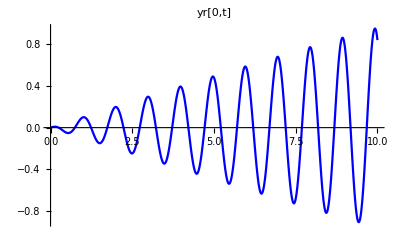

δk = 0.4

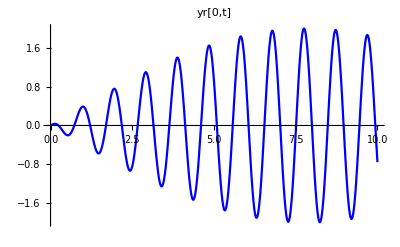

δk = 0.7

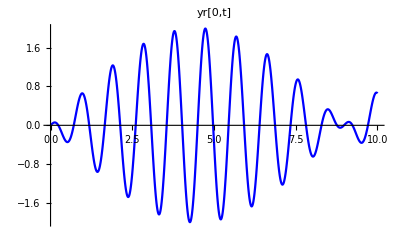

δk = 1.5

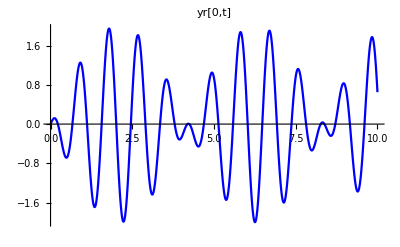

δk = 2.

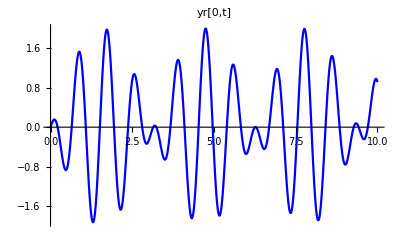

δk = 3.

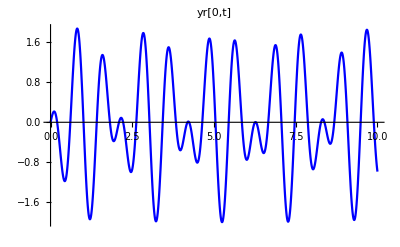

A2 = 1.2

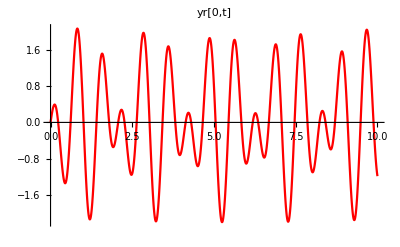

A2 = 2.

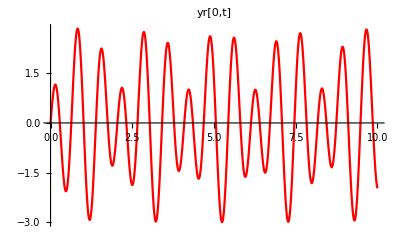

A2 = 5.

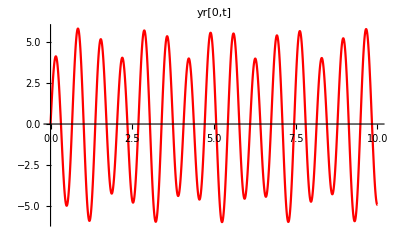

A2 = 6.

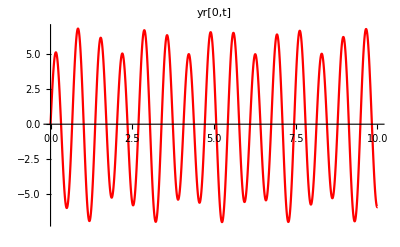

A person standing at x=10 would hear beats from the two interfering waves. That is, he would hear a pitch with a periodic change in volume.

```mathematica
(*2*)

(* i *)

A1=1;
A2=1;
δklist={.1,.4,.7,1.5,2.0,3.0};


For[i=1,i<Length[δklist]+1,i++,
k2=k1+δklist[[i]];
Print["δk = ",δklist[[i]]];
Print[Plot[yr[0,t],{t,0,10},PlotStyle->Blue,PlotLabel->"yr[0,t]"]]
]

(* ii *)

δk=.6;
A2list={1.2,2.0,5.0,6.0};

For[i=1,i<Length[A2list]+1,i++,
Print["A2 = ",A2list[[i]]];
A2=A2list[[i]];
Print[Plot[yr[0,t],{t,0,10},PlotStyle->Red,PlotLabel->"yr[0,t]"]]
]

(* iii *)

A2=2;
δk=.5;

Animate[Plot[yr[x,t],{x,5,15}],{t,0,10},AnimationRate->1,AnimationRunning->False]

Print["A person standing at x=10 would hear beats from the two interfering waves. That is, he would hear a pitch with a periodic change in volume."]
```

```mathematica
(* 3 *)
Remove["Global`*"]

(** Marion 13-21 **)

SetAttributes[{k0,ω0,δk,ω0p},Constant];
$Assumptions={Element[{k0,ω0,δk,ω0p,t},Reals] && k0>0 && ω0>0 && δk >0};

A[k_]:=Piecewise[{{1,Abs[k-k0]<Δk}},0] 

Ψ[x_,t_]:=Integrate[ A[k] E^(I (ω t - k x)),{k,- Infinity,Infinity}]//Simplify

Print["Ψ[x,0]= ",Real[Ψ[x,0]]]

(** k0=2Pi; **)
(** Δk=Pi; **)

(** Non-Marion Part **)

(* i *) A1[k_]:=DiracDelta[k-k0];
(* ii *) A2[k_]:=Piecewise[{{1,Abs[k-k0]<Δk}},0](** Isn't this the same thing as the Marion problem??? **)
(* iii *) A3[k_]:=Piecewise[{{Cos[Pi/(2Δk)](k-k0),Abs[k-k0]<Δk}},0]

(* iv *) A4[k_]:=Piecewise[{{(k-k0+Δk)/(2 Δk),Abs[k-k0]<Δk}},0]

(* v *) A5[k_]:=Piecewise[{{(k-k0)^2/Δk^2,Abs[k-k0]<Δk}},0]

Alist={A1[k],A2[k],A3[k],A4[k],A5[k]};

For[i=1,i<6,i++,
A[k]=Alist[[i]];
Print["\nFor A[k]= ",A[k],"\n Ψ[x,0]= ", Real[Ψ[x,0]]];
]

(** I'm not sure why but I can't figure out how to plot any of these. **)
```

Ψ[x,0]= Real[Piecewise[{{(2 ⅇ^(-ⅈ k0 x) Sin[x Δk])/x, Δk>0}, {0, True}}]]

For A[k]= DiracDelta[k-k0]
 Ψ[x,0]= Real[ⅇ^(-ⅈ k0 x)]

For A[k]= Piecewise[{{1, Abs[k-k0]<Δk}, {0, True}}]
 Ψ[x,0]= Real[Piecewise[{{(2 ⅇ^(-ⅈ k0 x) Sin[x Δk])/x, Δk>0}, {0, True}}]]

For A[k]= Piecewise[{{(k-k0) Cos[π/(2 Δk)], Abs[k-k0]<Δk}, {0, True}}]
 Ψ[x,0]= Real[Piecewise[{{(2 ⅈ ⅇ^(-ⅈ k0 x) Cos[π/(2 Δk)] (x Δk Cos[x Δk]-Sin[x Δk]))/x^2, Δk>0}, {0, True}}]]

For A[k]= Piecewise[{{(k-k0+Δk)/(2 Δk), Abs[k-k0]<Δk}, {0, True}}]
 Ψ[x,0]= Real[Piecewise[{{(ⅇ^(-ⅈ x (k0+Δk)) (1-ⅇ^(2 ⅈ x Δk)+2 ⅈ x Δk))/(2 x^2 Δk), Δk>0}, {0, True}}]]

For A[k]= Piecewise[{{(k-k0)^2/Δk^2, Abs[k-k0]<Δk}, {0, True}}]
 Ψ[x,0]= Real[Piecewise[{{-ⅇ^(-ⅈ k0 x) Δk (ExpIntegralE[-2,-ⅈ x Δk]+ExpIntegralE[-2,ⅈ x Δk]), Δk>0}, {0, True}}]]

```mathematica
(* 4 *)

(** Marion 13-2 **)

$Assumptions={Element[L,Reals]&& τ>0 && ρ>0};

(** Inital conditions for the string **)
q[x,0]=Piecewise[{{(3h)/L x,0≤x ≤L/3},{(3h)/(2L)(L-x),L/3≤x≤L}}];

q'[x,0]=0;

ω[n_]=(π n)/L Sqrt[τ/ρ];

A[n_]=2/L Integrate[q[x,0] Sin[(n π x)/L],{x,0,L}]//Simplify;

A[n_]=A[n][[1,1,1]];(** Get's rid of the piecewise part **)

Print["\n The A[n] for the sum are: ",A[n]]

B[n_]=-2/(ω[n]L)Integrate[q'[x,0] Sin[(n π x)/L],{x,0,L}]//Simplify;

Print["\n The B[n] for the sum are: ",B[n]]

q[x,t]=Sum[A[i]Sin[(i n π)/L]Cos[ω[i]t],{i,1,5}]; 

Print["\n The first few terms of the wave function for the string are:\n
q[x,t]= ",q[x,t]]
```

The A[n] for the sum are: (12 h Sin[(n π)/3]^3)/(n^2 π^2)

The B[n] for the sum are: 0

The first few terms of the wave function for the string are:

q[x,t]= (9 √3 h Cos[(π t √(τ/ρ))/L] Sin[(n π)/L])/(2 π^2)+(9 √3 h Cos[(2 π t √(τ/ρ))/L] Sin[(2 n π)/L])/(8 π^2)-(9 √3 h Cos[(4 π t √(τ/ρ))/L] Sin[(4 n π)/L])/(32 π^2)-(9 √3 h Cos[(5 π t √(τ/ρ))/L] Sin[(5 n π)/L])/(50 π^2)

We will demonstrate that was the width of f[x] decreases (i.e. α increases) the width of FT[ω] increases graphically by plotting f[x],FT[ω] for various values of α.

α = 1

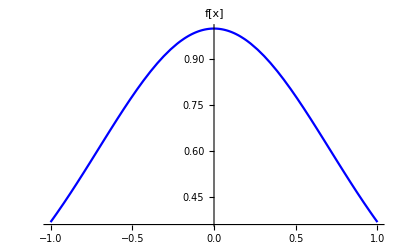

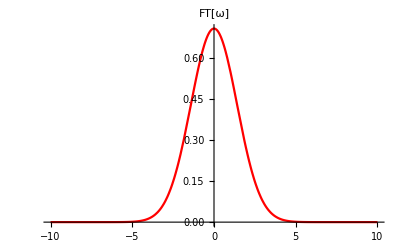

α = 5

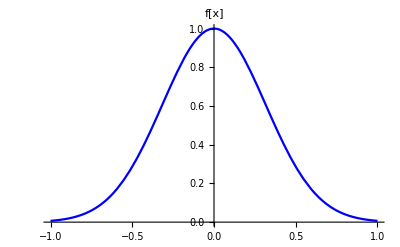

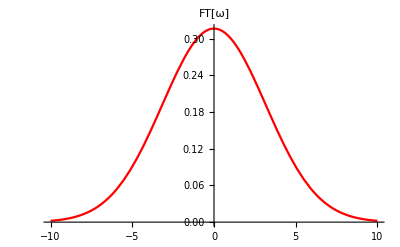

α = 10

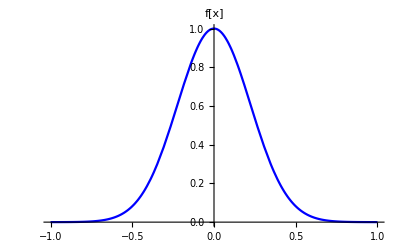

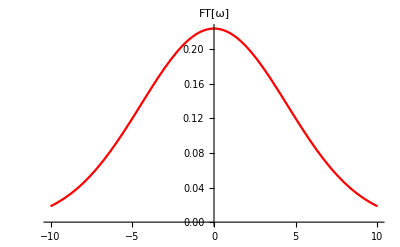

α = 15

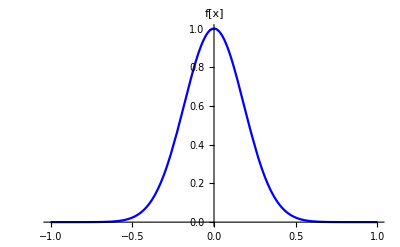

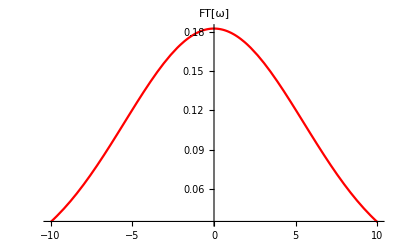

α = 20

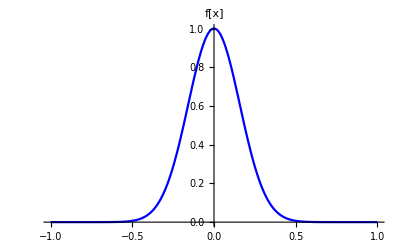

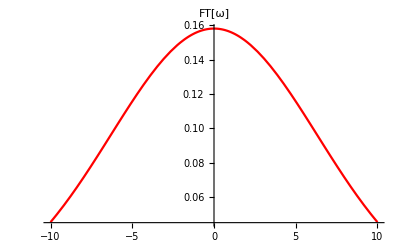

α = 35

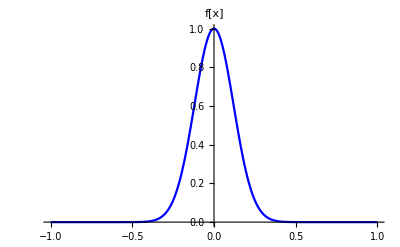

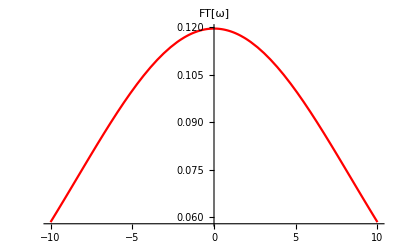

From the plots it is clear that as α incrases (width of f[x] decreases) the width of FT[ω] increases!

*******************************************************************

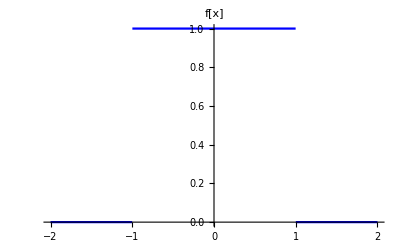

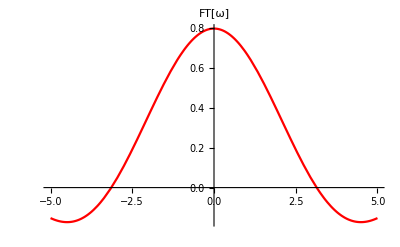

The QM interpretation of these graphics is just the uncertainty principle. Since we definitely know the position f[x] of some particle, we cannot definitely know it's momentum, as Δx Δp ≤ ℏ/2.

```mathematica
(* 5 *)

(* a *)
f[x_]:=M E^(-α x^2)
FT[ω_]:=FourierTransform[f[x],x,ω]

M=1; 

Print["We will demonstrate that was the width of f[x] decreases (i.e. α increases) the width of FT[ω] increases graphically by plotting f[x],FT[ω] for various values of α.\n"]

αlist= {1,5,10,15,20,35};

For[
i=1,i<Length[αlist]+1,i++,
α=αlist[[i]];
Print["α = ",αlist[[i]]];
Print[Plot[f[x],{x,-1,1},PlotLabel->"f[x]",PlotStyle->Blue]];
Print[Plot[FT[ω],{ω,-10,10},PlotLabel->"FT[ω]",PlotStyle->Red]]
]

Print["From the plots it is clear that as α incrases (width of f[x] decreases) the width of FT[ω] increases!"]

Print["*******************************************************************"]

(* b *)

Clear[f,FT]

f[x_]:=Piecewise[{{1,Abs[x]<a},{0,Abs[x]>a}}]

FT[ω_]:=FourierTransform[f[x],x,ω]

a=1;

Plot[f[x],{x,-2,2},PlotLabel->"f[x]",PlotStyle->Blue]
Plot[FT[ω],{ω,-5,5},PlotLabel->"FT[ω]",PlotStyle->Red]

Print["The QM interpretation of these graphics is just the uncertainty principle. Since we definitely know the position f[x] of some particle, we cannot definitely know it's momentum, as Δx Δp ≤ ℏ/2.\n"]
```

```mathematica
(* 6 *)
Clear[y1,y2,ω0,ω1,ω2]

y1[t_]:=Sin[ω0 t]
y2[t_]:=Sin[ω1 t]Sin[ω2 t]

A[k]=Alist[[5]];
Ψ5[x,0]:=Ψ[x,0];

FTy1[ω_]=FourierTransform[y1[t],t,ω];
FTy2[ω_]=FourierTransform[y2[t],t,ω];
FTΨ5[ω_]=FourierTransform[Ψ5[x,0],x,ω];

Print["\nThe Fourier Transform of y1[t]= ",y1[t]," is :\n"
,"FTy1[ω]= ",FTy1[ω]]

Print["\nThe Fourier Transform of y2[t]= ",y2[t]," is :\n"
,"FTy2[ω]= ",FTy2[ω]]
Print["\nThe Fourier Transform of Ψ5[x,0]= ",Ψ5[x,0]," is :\n"
,"FTΨ5[ω]= ",FTΨ5[ω]]
```

The Fourier Transform of y1[t]= Sin[t ω0] is :
FTy1[ω]= ⅈ √(π/2) DiracDelta[ω-ω0]-ⅈ √(π/2) DiracDelta[ω+ω0]

The Fourier Transform of y2[t]= Sin[t ω1] Sin[t ω2] is :
FTy2[ω]= -1/2 √(π/2) DiracDelta[ω-ω1-ω2]+1/2 √(π/2) DiracDelta[ω+ω1-ω2]+1/2 √(π/2) DiracDelta[ω-ω1+ω2]-1/2 √(π/2) DiracDelta[ω+ω1+ω2]

The Fourier Transform of Ψ5[x,0]= Piecewise[{{-ⅇ^(-ⅈ k0 x) Δk (ExpIntegralE[-2,-ⅈ x Δk]+ExpIntegralE[-2,ⅈ x Δk]), Δk>0}, {0, True}}] is :
FTΨ5[ω]= -(√(2 π) (k0-ω)^2 (-1+UnitStep[-Δk]))/Δk^2